Bernoulli distribution models the coin toss distribution:

```mathematica
PBernoulli[x_, θ_]:=θ^x(1-θ)^(1-x)
```

```mathematica
PBernoulli[1,0.6]
```

0.6

```mathematica
Mean[BernoulliDistribution[1/2]]
```

1/2

```mathematica
rand = RandomVariate[BernoulliDistribution[1/2],10000];
```

```mathematica
Count[rand,1]
```

5003

Example of Bernoulli distribution: 
Out of 10 bulbs one is defective, simulate production of 100 bulbs.

```mathematica
RandomVariate[BernoulliDistribution[9/10],100]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

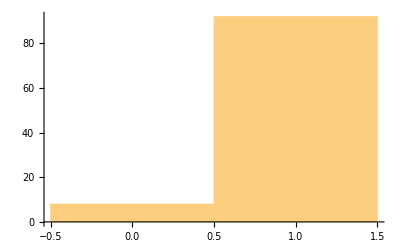

```mathematica
Histogram[%16]
```